Project root: /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits

Tables path:  /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables

Figures path: /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs

Logs path:    /Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/logs

<|01_gauge_covariance_numeric→True,02_nonabelian_convergence_numeric→True,03_frame_based_overlap_pipeline_numeric→True,04_feedforward_correction_numeric→True,05_conditioning_noise_sensitivity_slopes→True,05_conditioning_noise_sensitivity_fixed_eta→True|>

category | metric | value | note
01 gauge covariance | max_gauge_covariance_error | 9.54181×10^-15 | Should be near machine precision.
01 gauge covariance | max_unitarity_error | 1.44627×10^-14 | Should be near machine precision.
01 gauge covariance | min_overlap_singular_value | 0.948464 | Conditioning diagnostic.
02 non-Abelian convergence | initial_error_N_min | 0.0156618 | Frobenius error at smallest N.
02 non-Abelian convergence | final_error_N_max | 9.00881×10^-7 | Frobenius error at largest N.
02 non-Abelian convergence | estimated_order | 2.00849 | Computed from log-log fit.
02 non-Abelian convergence | max_unitarity_error | 3.24808×10^-14 | Discrete holonomy unitarity.
03 frame overlap pipeline | initial_error_N_min | 0.0932001 | Frobenius error at smallest N.
03 frame overlap pipeline | final_error_N_max | 5.66358×10^-6 | Frobenius error at largest N.
03 frame overlap pipeline | estimated_order | 2.00065 | Computed from log-log fit.
03 frame overlap pipeline | min_overlap_singular_value | 0.920739 | Conditioning diagnostic.
03 frame overlap pipeline | max_unitarity_error | 7.25621×10^-13 | Discrete holonomy unitarity.
03 frame overlap pipeline | initial_projector_step_distance | 0.551797 | Coarsest partition.
03 frame overlap pipeline | final_projector_step_distance | 0.00447215 | Finest partition.
03 frame overlap pipeline | projector_step_estimated_order | 0.99467 | Expected approximately first order.
03 frame overlap pipeline | max_frame_orthonormality_error | 3.23683×10^-16 | Frame sanity check.
03 frame overlap pipeline | max_closure_error | 3.08357×10^-16 | Closed-loop sanity check.
04 feed-forward correction | initial_holonomy_error | 0.0156618 | Smallest N.
04 feed-forward correction | final_holonomy_error | 9.00484×10^-7 | Largest N.
04 feed-forward correction | holonomy_estimated_order | 2.00855 | Computed from log-log fit.
04 feed-forward correction | left_initial_correction_error | 0.0156618 | Smallest N.
04 feed-forward correction | left_final_correction_error | 9.00484×10^-7 | Largest N.
04 feed-forward correction | left_correction_order | 2.00855 | Computed from log-log fit.
04 feed-forward correction | left_initial_fidelity | 0.999877 | Smallest N.
04 feed-forward correction | left_final_fidelity | 1. | Largest N.
04 feed-forward correction | right_initial_correction_error | 0.0156618 | Smallest N.
04 feed-forward correction | right_final_correction_error | 9.00484×10^-7 | Largest N.
04 feed-forward correction | right_correction_order | 2.00855 | Computed from log-log fit.
04 feed-forward correction | right_initial_fidelity | 0.999877 | Smallest N.
04 feed-forward correction | right_final_fidelity | 1. | Largest N.
04 feed-forward correction | max_holonomy_unitarity_error | 3.24808×10^-14 | Estimated holonomy unitarity.
04 feed-forward correction | left_max_corrected_unitarity_error | 3.24058×10^-14 | Corrected gate unitarity.
04 feed-forward correction | right_max_corrected_unitarity_error | 3.23995×10^-14 | Corrected gate unitarity.
05 conditioning/noise | mean_scaled_noise_slope | 1.00159 | Mean slope of error vs eta/mu.
05 conditioning/noise | min_scaled_noise_slope | 0.946979 | Across controlled conditioning values.
05 conditioning/noise | max_scaled_noise_slope | 1.06607 | Across controlled conditioning values.
05 conditioning/noise | fixed_eta_conditioning_slope | 0.364452 | Slope of error vs eta/mu at fixed eta.
05 conditioning/noise | fixed_eta_max_unitarity_error | 1.5813×10^-14 | Noisy-overlap holonomy unitarity.

result | value
max gauge covariance residual | 9.54181×10^-15
max gauge-run unitarity residual | 1.44627×10^-14
non-Abelian convergence order | 2.00849
non-Abelian error N_min | 0.0156618
non-Abelian error N_max | 9.00881×10^-7
frame-pipeline convergence order | 2.00065
frame-pipeline error N_min | 0.0932001
frame-pipeline error N_max | 5.66358×10^-6
frame-pipeline min overlap singular value | 0.920739
feed-forward holonomy convergence order | 2.00855
left correction convergence order | 2.00855
right correction convergence order | 2.00855
left final correction fidelity | 1.
right final correction fidelity | 1.
mean scaled-noise slope | 1.00159
fixed-eta conditioning slope | 0.364452

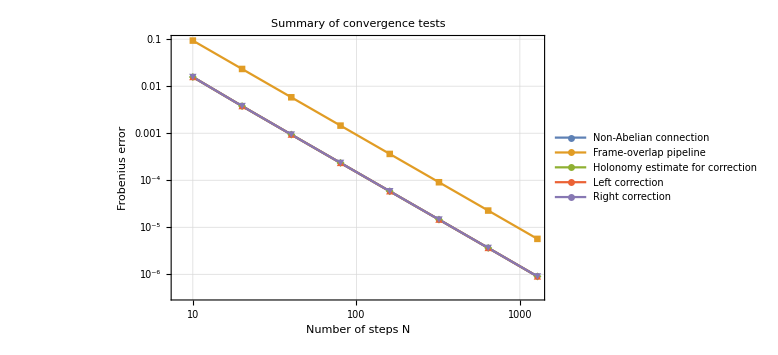

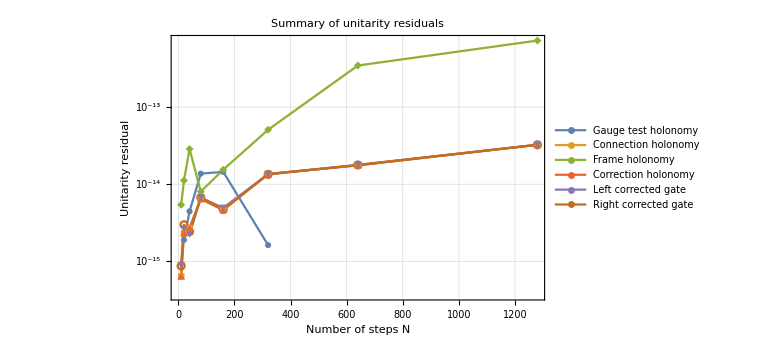

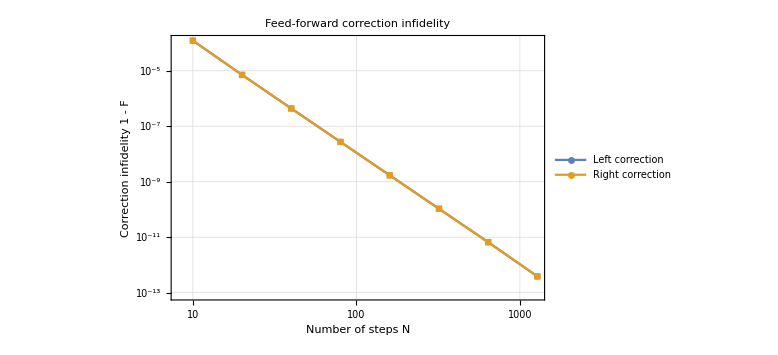

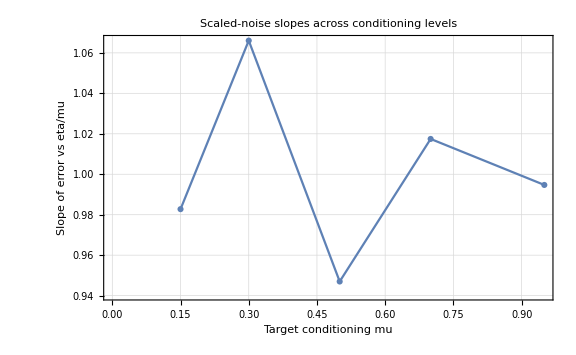

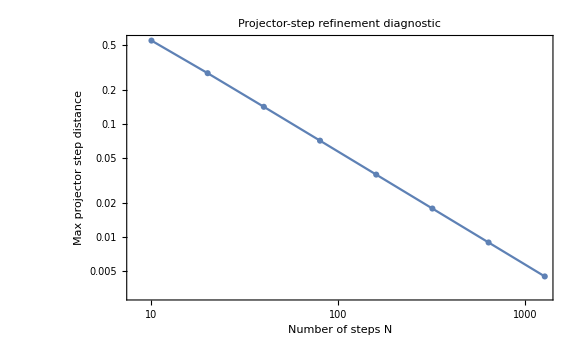

<|gauge_covariance_residual_small→True,gauge_unitarity_residual_small→True,nonabelian_error_decreases→True,frame_pipeline_error_decreases→True,frame_projector_step_decreases→True,left_correction_error_decreases→True,right_correction_error_decreases→True,left_final_fidelity_near_one→True,right_final_fidelity_near_one→True,scaled_noise_slopes_near_one→True|>

PASS

06_validation_summary.nb completed.

Purpose:
Aggregate validation outputs from notebooks 01--05.

Overall validation status:
PASS

Validation checks:
<|"gauge_covariance_residual_small" -> True, "gauge_unitarity_residual_small" -> True, "nonabelian_error_decreases" -> True, "frame_pipeline_error_decreases" -> True, "frame_projector_step_decreases" -> True, "left_correction_error_decreases" -> True, "right_correction_error_decreases" -> True, "left_final_fidelity_near_one" -> True, "right_final_fidelity_near_one" -> True, "scaled_noise_slopes_near_one" -> True|>

Paper metrics:
{{"result", "value"}, {"max gauge covariance residual", 9.54180670278024*^-15}, {"max gauge-run unitarity residual", 1.4462699960145175*^-14}, {"non-Abelian convergence order", 2.008490030704305}, {"non-Abelian error N_min", 0.015661771106194062}, {"non-Abelian error N_max", 9.008810419080525*^-7}, {"frame-pipeline convergence order", 2.000645142347237}, {"frame-pipeline error N_min", 0.09320009376342507}, {"frame-pipeline error N_max", 5.6635751712933615*^-6}, {"frame-pipeline min overlap singular value", 0.920738915091769}, {"feed-forward holonomy convergence order", 2.0085454156994187}, {"left correction convergence order", 2.0085454156911657}, {"right correction convergence order", 2.008545415707916}, {"left final correction fidelity", 0.999999999999615}, {"right final correction fidelity", 0.9999999999996152}, {"mean scaled-noise slope", 1.0015931081858414}, {"fixed-eta conditioning slope", 0.36445151841198653}}

Generated files:
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/06_validation_summary_key_metrics.csv
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/06_validation_summary_paper_metrics.csv
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/06_summary_convergence_tests.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/06_summary_convergence_tests.png
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/06_summary_unitarity_residuals.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/06_summary_unitarity_residuals.png
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/06_summary_correction_infidelity.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/06_summary_correction_infidelity.png
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/06_summary_noise_slopes.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/06_summary_noise_slopes.png
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/06_summary_projector_refinement.pdf
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/figs/06_summary_projector_refinement.png

Project root:
/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits

<|overall_status→PASS,validation_checks→<|gauge_covariance_residual_small→True,gauge_unitarity_residual_small→True,nonabelian_error_decreases→True,frame_pipeline_error_decreases→True,frame_projector_step_decreases→True,left_correction_error_decreases→True,right_correction_error_decreases→True,left_final_fidelity_near_one→True,right_final_fidelity_near_one→True,scaled_noise_slopes_near_one→True|>,max_gauge_covariance_error→9.54181×10^-15,nonabelian_convergence_order→2.00849,frame_pipeline_convergence_order→2.00065,left_correction_order→2.00855,right_correction_order→2.00855,mean_scaled_noise_slope→1.00159,key_metrics_csv→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/06_validation_summary_key_metrics.csv,paper_metrics_csv→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/tables/06_validation_summary_paper_metrics.csv,log→/Users/njblost/GitHub/Non-Abelian-Wilczek-Zee-holonomy-calibration-and-feed-forward-for-time-bin-qudits/results/logs/06_validation_summary_log.txt|>

```mathematica
(*06—Validation Summary*)

(*This notebook aggregates the results from notebooks 01--05. It imports the generated CSV tables,computes compact summary metrics,produces summary plots,and exports a final validation-summary table and log for the repository.*)

(*Initialization*)
ClearAll["Global`*"];

rootPath=ParentDirectory[NotebookDirectory[]];

SetDirectory[rootPath];
Get[FileNameJoin[{rootPath,"src","HolonomyTools.wl"}]];

(*HolonomyTools.wl clears Global`*,so re-define paths after loading.*)
rootPath=ParentDirectory[NotebookDirectory[]];
SetDirectory[rootPath];

resultsPath=FileNameJoin[{rootPath,"results"}];
tablesPath=FileNameJoin[{rootPath,"results","tables"}];
figsPath=FileNameJoin[{rootPath,"results","figs"}];
logsPath=FileNameJoin[{rootPath,"results","logs"}];

Do[If[!DirectoryQ[dir],CreateDirectory[dir,CreateIntermediateDirectories->True]],{dir,{resultsPath,tablesPath,figsPath,logsPath}}];

ClearAll[localExportCSV,localExportTXT,localExportFIG];

localExportCSV[name_String,data_]:=Module[{path},path=FileNameJoin[{tablesPath,name}];
Export[path,data,"CSV"];
path];

localExportTXT[name_String,text_String]:=Module[{path},path=FileNameJoin[{logsPath,name}];
Export[path,text,"Text"];
path];

localExportFIG[name_String,fig_]:=Module[{path},path=FileNameJoin[{figsPath,name}];
Export[path,fig];
path];

Print["Project root: ",rootPath];
Print["Tables path:  ",tablesPath];
Print["Figures path: ",figsPath];
Print["Logs path:    ",logsPath];

(*Import and parsing utilities*)

ClearAll[tablePath,importCSV,toNumericCell,numericRows,assertNumericMatrix,positivePairs,logLogSlope,finiteNumberQ];

tablePath[name_String]:=FileNameJoin[{tablesPath,name}];

importCSV[name_String]:=Module[{path},path=tablePath[name];
If[!FileExistsQ[path],Print["Missing file: ",path];
Return[$Failed]];
Import[path,"CSV"]];

finiteNumberQ[x_]:=NumberQ[x]&&x=!=Indeterminate&&x=!=ComplexInfinity&&x=!=DirectedInfinity[1]&&x=!=DirectedInfinity[-1];

toNumericCell[x_]:=Module[{s,y},Which[NumberQ[x],N[x],StringQ[x],s=StringTrim[x];
If[s===""||s==="NA"||s==="NaN",Missing["NotNumeric"],Quiet[Check[y=ToExpression[s];
If[NumberQ[y],N[y],Missing["NotNumeric"]],Missing["NotNumeric"]]]],True,Missing["NotNumeric"]]];

(*Correct parsing:convert each cell of each data row,not each row as a whole.*)
numericRows[table_List]:=(toNumericCell/@#)&/@Rest[table];

assertNumericMatrix[name_String,rows_List]:=Module[{bad},bad=Select[rows,!VectorQ[#,finiteNumberQ]&];
If[Length[bad]>0,Print["Non-numeric rows found in ",name,":"];
Print[bad//Short];
Return[False],Return[True]]];

positivePairs[rows_List,xcol_Integer,ycol_Integer]:=Select[rows[[All,{xcol,ycol}]],finiteNumberQ[#[[1]]]&&finiteNumberQ[#[[2]]]&&#[[1]]>0&&#[[2]]>0&];

logLogSlope[rows_List,xcol_Integer,ycol_Integer]:=Module[{pairs,fit,slope},pairs=positivePairs[rows,xcol,ycol];
If[Length[pairs]<2,Return[Missing["InsufficientData"]]];
fit=LinearModelFit[({Log[#[[1]]],Log[#[[2]]]}&/@pairs),x,x];
slope=fit["BestFitParameters"][[2]];
slope];

(*Import all numeric validation tables*)

gaugeTableRaw=importCSV["01_gauge_covariance_numeric.csv"];
nonAbelianTableRaw=importCSV["02_nonabelian_convergence_numeric.csv"];
frameTableRaw=importCSV["03_frame_based_overlap_pipeline_numeric.csv"];
feedforwardTableRaw=importCSV["04_feedforward_correction_numeric.csv"];
noiseSlopesTableRaw=importCSV["05_conditioning_noise_sensitivity_slopes.csv"];
fixedEtaTableRaw=importCSV["05_conditioning_noise_sensitivity_fixed_eta.csv"];

If[MemberQ[{gaugeTableRaw,nonAbelianTableRaw,frameTableRaw,feedforwardTableRaw,noiseSlopesTableRaw,fixedEtaTableRaw},$Failed],Print["One or more required input tables are missing. Run notebooks 01--05 first."];
Abort[]];

gaugeRows=numericRows[gaugeTableRaw];
nonAbelianRows=numericRows[nonAbelianTableRaw];
frameRows=numericRows[frameTableRaw];
feedforwardRows=numericRows[feedforwardTableRaw];
noiseSlopeRows=numericRows[noiseSlopesTableRaw];
fixedEtaRows=numericRows[fixedEtaTableRaw];

numericImportChecks=<|"01_gauge_covariance_numeric"->assertNumericMatrix["01_gauge_covariance_numeric.csv",gaugeRows],"02_nonabelian_convergence_numeric"->assertNumericMatrix["02_nonabelian_convergence_numeric.csv",nonAbelianRows],"03_frame_based_overlap_pipeline_numeric"->assertNumericMatrix["03_frame_based_overlap_pipeline_numeric.csv",frameRows],"04_feedforward_correction_numeric"->assertNumericMatrix["04_feedforward_correction_numeric.csv",feedforwardRows],"05_conditioning_noise_sensitivity_slopes"->assertNumericMatrix["05_conditioning_noise_sensitivity_slopes.csv",noiseSlopeRows],"05_conditioning_noise_sensitivity_fixed_eta"->assertNumericMatrix["05_conditioning_noise_sensitivity_fixed_eta.csv",fixedEtaRows]|>;

numericImportChecks

If[!And@@Values[numericImportChecks],Print["Stopping because one or more imported tables contain nonnumeric rows."];
Abort[]];

(*Compute summary metrics*)

(*01 Gauge covariance table columns:1 N 2 gauge_covariance_error 3 unitarity_error 4 min_singular_value*)

maxGaugeCovarianceError=Max[gaugeRows[[All,2]]];
maxGaugeUnitarityError=Max[gaugeRows[[All,3]]];
minGaugeSingularValue=Min[gaugeRows[[All,4]]];

(*02 Non-Abelian convergence table columns:1 N 2 frobenius_error_to_continuum_reference 3 unitarity_error*)

nonAbelianInitialError=First[nonAbelianRows][[2]];
nonAbelianFinalError=Last[nonAbelianRows][[2]];
nonAbelianMaxUnitarityError=Max[nonAbelianRows[[All,3]]];
nonAbelianSlope=logLogSlope[nonAbelianRows,1,2];
nonAbelianOrder=-nonAbelianSlope;

(*03 Frame-based overlap table columns:1 N 2 frobenius_error_to_exact_reference 3 unitarity_error 4 min_singular_value 5 max_projector_step_distance 6 max_frame_orthonormality_error 7 frame_closure_error*)

frameInitialError=First[frameRows][[2]];
frameFinalError=Last[frameRows][[2]];
frameMaxUnitarityError=Max[frameRows[[All,3]]];
frameMinSingularValue=Min[frameRows[[All,4]]];
frameInitialProjectorStep=First[frameRows][[5]];
frameFinalProjectorStep=Last[frameRows][[5]];
frameMaxOrthonormalityError=Max[frameRows[[All,6]]];
frameMaxClosureError=Max[frameRows[[All,7]]];
frameSlope=logLogSlope[frameRows,1,2];
frameOrder=-frameSlope;
projectorStepSlope=logLogSlope[frameRows,1,5];
projectorStepOrder=-projectorStepSlope;

(*04 Feed-forward correction table columns:1 N 2 holonomy_frobenius_error 3 estimated_holonomy_unitarity_error 4 left_correction_error 5 left_correction_fidelity 6 left_corrected_unitarity_error 7 right_correction_error 8 right_correction_fidelity 9 right_corrected_unitarity_error*)

feedInitialHolonomyError=First[feedforwardRows][[2]];
feedFinalHolonomyError=Last[feedforwardRows][[2]];
feedMaxHolonomyUnitarityError=Max[feedforwardRows[[All,3]]];

leftInitialCorrectionError=First[feedforwardRows][[4]];
leftFinalCorrectionError=Last[feedforwardRows][[4]];
leftInitialFidelity=First[feedforwardRows][[5]];
leftFinalFidelity=Last[feedforwardRows][[5]];
leftMaxCorrectedUnitarityError=Max[feedforwardRows[[All,6]]];

rightInitialCorrectionError=First[feedforwardRows][[7]];
rightFinalCorrectionError=Last[feedforwardRows][[7]];
rightInitialFidelity=First[feedforwardRows][[8]];
rightFinalFidelity=Last[feedforwardRows][[8]];
rightMaxCorrectedUnitarityError=Max[feedforwardRows[[All,9]]];

feedHolonomySlope=logLogSlope[feedforwardRows,1,2];
feedHolonomyOrder=-feedHolonomySlope;

leftCorrectionSlope=logLogSlope[feedforwardRows,1,4];
leftCorrectionOrder=-leftCorrectionSlope;

rightCorrectionSlope=logLogSlope[feedforwardRows,1,7];
rightCorrectionOrder=-rightCorrectionSlope;

(*05 Noise slopes table columns:1 target_mu 2 actual_mu_min 3 log_log_slope_error_vs_rho 4 estimated_noise_order*)

noiseSlopeValues=noiseSlopeRows[[All,3]];
noiseSlopeMean=Mean[noiseSlopeValues];
noiseSlopeMin=Min[noiseSlopeValues];
noiseSlopeMax=Max[noiseSlopeValues];

(*05 Fixed-eta table columns:1 target_mu 2 actual_mu_min 3 N_base 4 eta 5 mu_min_used 6 eta_over_mu 7 mean_holonomy_error 8 std_holonomy_error 9 mean_unitarity_error 10 max_unitarity_error 11 trials*)

fixedEtaConditioningSlope=logLogSlope[({#[[6]],#[[7]]}&/@fixedEtaRows),1,2];

fixedEtaMaxUnitarityError=Max[fixedEtaRows[[All,10]]];

(*Readable summary tables*)

keyMetrics={{"category","metric","value","note"},{"01 gauge covariance","max_gauge_covariance_error",maxGaugeCovarianceError,"Should be near machine precision."},{"01 gauge covariance","max_unitarity_error",maxGaugeUnitarityError,"Should be near machine precision."},{"01 gauge covariance","min_overlap_singular_value",minGaugeSingularValue,"Conditioning diagnostic."},{"02 non-Abelian convergence","initial_error_N_min",nonAbelianInitialError,"Frobenius error at smallest N."},{"02 non-Abelian convergence","final_error_N_max",nonAbelianFinalError,"Frobenius error at largest N."},{"02 non-Abelian convergence","estimated_order",nonAbelianOrder,"Computed from log-log fit."},{"02 non-Abelian convergence","max_unitarity_error",nonAbelianMaxUnitarityError,"Discrete holonomy unitarity."},{"03 frame overlap pipeline","initial_error_N_min",frameInitialError,"Frobenius error at smallest N."},{"03 frame overlap pipeline","final_error_N_max",frameFinalError,"Frobenius error at largest N."},{"03 frame overlap pipeline","estimated_order",frameOrder,"Computed from log-log fit."},{"03 frame overlap pipeline","min_overlap_singular_value",frameMinSingularValue,"Conditioning diagnostic."},{"03 frame overlap pipeline","max_unitarity_error",frameMaxUnitarityError,"Discrete holonomy unitarity."},{"03 frame overlap pipeline","initial_projector_step_distance",frameInitialProjectorStep,"Coarsest partition."},{"03 frame overlap pipeline","final_projector_step_distance",frameFinalProjectorStep,"Finest partition."},{"03 frame overlap pipeline","projector_step_estimated_order",projectorStepOrder,"Expected approximately first order."},{"03 frame overlap pipeline","max_frame_orthonormality_error",frameMaxOrthonormalityError,"Frame sanity check."},{"03 frame overlap pipeline","max_closure_error",frameMaxClosureError,"Closed-loop sanity check."},{"04 feed-forward correction","initial_holonomy_error",feedInitialHolonomyError,"Smallest N."},{"04 feed-forward correction","final_holonomy_error",feedFinalHolonomyError,"Largest N."},{"04 feed-forward correction","holonomy_estimated_order",feedHolonomyOrder,"Computed from log-log fit."},{"04 feed-forward correction","left_initial_correction_error",leftInitialCorrectionError,"Smallest N."},{"04 feed-forward correction","left_final_correction_error",leftFinalCorrectionError,"Largest N."},{"04 feed-forward correction","left_correction_order",leftCorrectionOrder,"Computed from log-log fit."},{"04 feed-forward correction","left_initial_fidelity",leftInitialFidelity,"Smallest N."},{"04 feed-forward correction","left_final_fidelity",leftFinalFidelity,"Largest N."},{"04 feed-forward correction","right_initial_correction_error",rightInitialCorrectionError,"Smallest N."},{"04 feed-forward correction","right_final_correction_error",rightFinalCorrectionError,"Largest N."},{"04 feed-forward correction","right_correction_order",rightCorrectionOrder,"Computed from log-log fit."},{"04 feed-forward correction","right_initial_fidelity",rightInitialFidelity,"Smallest N."},{"04 feed-forward correction","right_final_fidelity",rightFinalFidelity,"Largest N."},{"04 feed-forward correction","max_holonomy_unitarity_error",feedMaxHolonomyUnitarityError,"Estimated holonomy unitarity."},{"04 feed-forward correction","left_max_corrected_unitarity_error",leftMaxCorrectedUnitarityError,"Corrected gate unitarity."},{"04 feed-forward correction","right_max_corrected_unitarity_error",rightMaxCorrectedUnitarityError,"Corrected gate unitarity."},{"05 conditioning/noise","mean_scaled_noise_slope",noiseSlopeMean,"Mean slope of error vs eta/mu."},{"05 conditioning/noise","min_scaled_noise_slope",noiseSlopeMin,"Across controlled conditioning values."},{"05 conditioning/noise","max_scaled_noise_slope",noiseSlopeMax,"Across controlled conditioning values."},{"05 conditioning/noise","fixed_eta_conditioning_slope",fixedEtaConditioningSlope,"Slope of error vs eta/mu at fixed eta."},{"05 conditioning/noise","fixed_eta_max_unitarity_error",fixedEtaMaxUnitarityError,"Noisy-overlap holonomy unitarity."}};

Grid[keyMetrics,Frame->All,Alignment->Left,ItemSize->All]

paperMetrics={{"result","value"},{"max gauge covariance residual",maxGaugeCovarianceError},{"max gauge-run unitarity residual",maxGaugeUnitarityError},{"non-Abelian convergence order",nonAbelianOrder},{"non-Abelian error N_min",nonAbelianInitialError},{"non-Abelian error N_max",nonAbelianFinalError},{"frame-pipeline convergence order",frameOrder},{"frame-pipeline error N_min",frameInitialError},{"frame-pipeline error N_max",frameFinalError},{"frame-pipeline min overlap singular value",frameMinSingularValue},{"feed-forward holonomy convergence order",feedHolonomyOrder},{"left correction convergence order",leftCorrectionOrder},{"right correction convergence order",rightCorrectionOrder},{"left final correction fidelity",leftFinalFidelity},{"right final correction fidelity",rightFinalFidelity},{"mean scaled-noise slope",noiseSlopeMean},{"fixed-eta conditioning slope",fixedEtaConditioningSlope}};

Grid[paperMetrics,Frame->All,Alignment->Left,ItemSize->All]

(*Summary plots*)

convergenceComparisonPlot=ListLogLogPlot[{positivePairs[nonAbelianRows,1,2],positivePairs[frameRows,1,2],positivePairs[feedforwardRows,1,2],positivePairs[feedforwardRows,1,4],positivePairs[feedforwardRows,1,7]},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","Frobenius error"},PlotLegends->{"Non-Abelian connection","Frame-overlap pipeline","Holonomy estimate for correction","Left correction","Right correction"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Summary of convergence tests"];

convergenceComparisonPlot

unitaritySummaryPlot=ListLogPlot[{positivePairs[gaugeRows,1,3],positivePairs[nonAbelianRows,1,3],positivePairs[frameRows,1,3],positivePairs[feedforwardRows,1,3],positivePairs[feedforwardRows,1,6],positivePairs[feedforwardRows,1,9]},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","Unitarity residual"},PlotLegends->{"Gauge test holonomy","Connection holonomy","Frame holonomy","Correction holonomy","Left corrected gate","Right corrected gate"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Summary of unitarity residuals"];

unitaritySummaryPlot

fidelitySummaryPlot=ListLogLogPlot[{({#[[1]],Max[1-#[[5]],10^-18]}&/@feedforwardRows),({#[[1]],Max[1-#[[8]],10^-18]}&/@feedforwardRows)},Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","Correction infidelity 1 - F"},PlotLegends->{"Left correction","Right correction"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Feed-forward correction infidelity"];

fidelitySummaryPlot

noiseSlopePlot=ListLinePlot[noiseSlopeRows[[All,{1,3}]],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Target conditioning mu","Slope of error vs eta/mu"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Scaled-noise slopes across conditioning levels"];

noiseSlopePlot

projectorSummaryPlot=ListLogLogPlot[positivePairs[frameRows,1,5],Joined->True,PlotMarkers->Automatic,Frame->True,FrameLabel->{"Number of steps N","Max projector step distance"},GridLines->Automatic,ImageSize->Large,PlotLabel->"Projector-step refinement diagnostic"];

projectorSummaryPlot

(*Export summary tables and figures*)

csvPathKeyMetrics=localExportCSV["06_validation_summary_key_metrics.csv",keyMetrics];

csvPathPaperMetrics=localExportCSV["06_validation_summary_paper_metrics.csv",paperMetrics];

figPathConvergencePDF=localExportFIG["06_summary_convergence_tests.pdf",convergenceComparisonPlot];

figPathConvergencePNG=localExportFIG["06_summary_convergence_tests.png",convergenceComparisonPlot];

figPathUnitarityPDF=localExportFIG["06_summary_unitarity_residuals.pdf",unitaritySummaryPlot];

figPathUnitarityPNG=localExportFIG["06_summary_unitarity_residuals.png",unitaritySummaryPlot];

figPathFidelityPDF=localExportFIG["06_summary_correction_infidelity.pdf",fidelitySummaryPlot];

figPathFidelityPNG=localExportFIG["06_summary_correction_infidelity.png",fidelitySummaryPlot];

figPathNoisePDF=localExportFIG["06_summary_noise_slopes.pdf",noiseSlopePlot];

figPathNoisePNG=localExportFIG["06_summary_noise_slopes.png",noiseSlopePlot];

figPathProjectorPDF=localExportFIG["06_summary_projector_refinement.pdf",projectorSummaryPlot];

figPathProjectorPNG=localExportFIG["06_summary_projector_refinement.png",projectorSummaryPlot];

(*Validation status*)

validationChecks=<|"gauge_covariance_residual_small"->(maxGaugeCovarianceError<10^-12),"gauge_unitarity_residual_small"->(maxGaugeUnitarityError<10^-12),"nonabelian_error_decreases"->(nonAbelianFinalError<nonAbelianInitialError),"frame_pipeline_error_decreases"->(frameFinalError<frameInitialError),"frame_projector_step_decreases"->(frameFinalProjectorStep<frameInitialProjectorStep),"left_correction_error_decreases"->(leftFinalCorrectionError<leftInitialCorrectionError),"right_correction_error_decreases"->(rightFinalCorrectionError<rightInitialCorrectionError),"left_final_fidelity_near_one"->(leftFinalFidelity>0.999),"right_final_fidelity_near_one"->(rightFinalFidelity>0.999),"scaled_noise_slopes_near_one"->And@@((0.8<#<1.2)&/@noiseSlopeValues)|>;

validationChecks

overallStatus=If[And@@Values[validationChecks],"PASS","CHECK"];

overallStatus

(*Export log*)

logText=StringRiffle[{"06_validation_summary.nb completed.","","Purpose:","Aggregate validation outputs from notebooks 01--05.","","Overall validation status:",overallStatus,"","Validation checks:",ToString[validationChecks,InputForm],"","Paper metrics:",ToString[paperMetrics,InputForm],"","Generated files:",csvPathKeyMetrics,csvPathPaperMetrics,figPathConvergencePDF,figPathConvergencePNG,figPathUnitarityPDF,figPathUnitarityPNG,figPathFidelityPDF,figPathFidelityPNG,figPathNoisePDF,figPathNoisePNG,figPathProjectorPDF,figPathProjectorPNG,"","Project root:",rootPath},"\n"];

logPath=localExportTXT["06_validation_summary_log.txt",logText];

Print[logText];

(*Final notebook summary*)

summary=<|"overall_status"->overallStatus,"validation_checks"->validationChecks,"max_gauge_covariance_error"->maxGaugeCovarianceError,"nonabelian_convergence_order"->nonAbelianOrder,"frame_pipeline_convergence_order"->frameOrder,"left_correction_order"->leftCorrectionOrder,"right_correction_order"->rightCorrectionOrder,"mean_scaled_noise_slope"->noiseSlopeMean,"key_metrics_csv"->csvPathKeyMetrics,"paper_metrics_csv"->csvPathPaperMetrics,"log"->logPath|>;

summary
```